```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with e^ik bc *)
hk[k_,n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->Exp[I k]tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* take a renormalization path (seq), a site label (i) and an approximant size (n) and return the new renormalization path, the new site label and the new size after one renormalization group operation *)
ClearAll[i,n];
iterSeq[{seq_,i_,n_}]:=Block[{inew=i,seqn=seq,nnew=n},
If[i>Fibonacci[n-1],seqn="m"<>seq;inew=i-Fibonacci[n-1];nnew=n-2;,
If[i>Fibonacci[n-2],seqn="a"<>seq;inew=i-Fibonacci[n-2];nnew=n-3,
seqn="m"<>seq;nnew=n-2;]];
{seqn,inew,nnew}
]
```

```mathematica
(* false when n<3 *)
test=#[[3]]≥3&;
(* variant where we forget about the site number *)
path2[i_,n_]:=NestWhile[iterSeq,{"",i,n},test][[1]]
```

```mathematica
(* Display all the paths for a system size *)
paths[n_]:=path2[#,n]&/@Range[Fibonacci[n]]
xPath[i_,n_]:=StringCount[NestWhile[iterSeq,{"",i,n},test][[1]],"m"]
tree[n_]:=xPath[#,n]&/@ Range[Fibonacci[n]]
```

```mathematica
(* compute intensity numerically, at finite ρ *)
ρ=0.1;
n=13;
{valp,vecp}=Eigensystem[hk[0.,n,ρ,1.]];
{valm,vecm}=Eigensystem[hk[N[Pi/2],n,ρ,1.]];
{vala,veca}=Eigensystem[hk[N[Pi],n,ρ,1.]];
val={valp,valm,vala};
vec={vecp,vecm,veca};
int={};
For[i=1,i<4,i++,
curval=val[[i]];
curvec=vec[[i]];
o=Ordering[curval];
val[[i]]=curval[[o]];
vec[[i]]=curvec[[o]];
AppendTo[int,Abs[vec[[i]]]^2];
]

(* evaluate the integral over k using Simpson's method *)
intm=(int[[1]]+4 int[[2]]+int[[3]])/6;

(* generate the list of positions where the intensity is nonzero at zero order *)
p=paths[n+2];
t=tree[n+2];
(* at first order there is intensity only at positions whose renormalization path matches the one of the corresponding energy level *)
m=Table[Flatten[Position[p,p[[a]]]],{a,Fibonacci[n+2]}];
```

```mathematica
(* evaluate λ numerically *)
lamb=Table[Total@(intm[[a,m[[a]]]]),{a,Length@intm}];
```

```mathematica
(* evaluate λ numerically *)
(* molecular sites in conumbering *)
mol=Range[Fibonacci[n]]~Join~Range[Fibonacci[n+1]+1,Fibonacci[n+2]];
lambmol=Table[Total@(intm[[a,mol]]),{a,mol}];
(* atomic sites *)
at=Range[Fibonacci[n]+1,Fibonacci[n+1]];
lambat=Table[Total@(intm[[a,at]]),{a,at}];
```

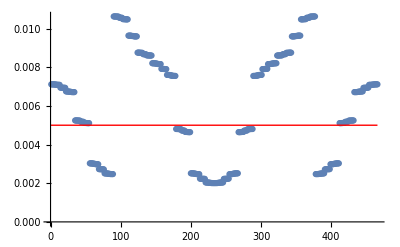

```mathematica
ListPlot[1-lambmol,PlotRange->All,Epilog->{Thick,Red,Line[{{0,ρ^2/2},{2Fibonacci[n],ρ^2/2}}]}]
```

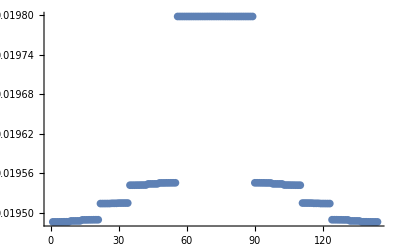

```mathematica
ListPlot[1-lambat,PlotRange->All,Epilog->{Thick,Red,Line[{{1,2 ρ^2},{Fibonacci[n-1]+1,2 ρ^2}}]}]
```

#### Molecules

```mathematica
(* evaluate λ numerically, site by site *)
(* select molecular sites at molecular energies *)
mol=Range[Fibonacci[n]]~Join~Range[Fibonacci[n+1]+1,Fibonacci[n+2]];
molN=intm[[mol,mol]];
(* select atomic sites at atomic energies *)
at=Range[Fibonacci[n]+1,Fibonacci[n+1]];
atN=intm[[at,at]];

l=Length[molN]/2;
mol11=molN[[1;;l,1;;l]];
mol12=molN[[1;;l,l+1;;2l]];
mol21=molN[[l+1;;2l,1;;l]];
mol22=molN[[l+1;;2l,l+1;;2l]];

molN=(mol11+mol12+mol21+mol22)/4;
```

```mathematica
Total[(mol12-mol21)^2,2]
```

0.000342404

```mathematica
(* compute intensity numerically, at finite ρ *)
ρ=0.1;
n=13-2;
{valp,vecp}=Eigensystem[hk[0.,n,ρ,1.]];
{valm,vecm}=Eigensystem[hk[N[Pi/2],n,ρ,1.]];
{vala,veca}=Eigensystem[hk[N[Pi],n,ρ,1.]];
val={valp,valm,vala};
vec={vecp,vecm,veca};
int={};
For[i=1,i<4,i++,
curval=val[[i]];
curvec=vec[[i]];
o=Ordering[curval];
val[[i]]=curval[[o]];
vec[[i]]=curvec[[o]];
AppendTo[int,Abs[vec[[i]]]^2];
]

(* evaluate the integral over k using Simpson's method *)
intm=(int[[1]]+4 int[[2]]+int[[3]])/6;
```

```mathematica
comparemol=(2molN)/intm;
```

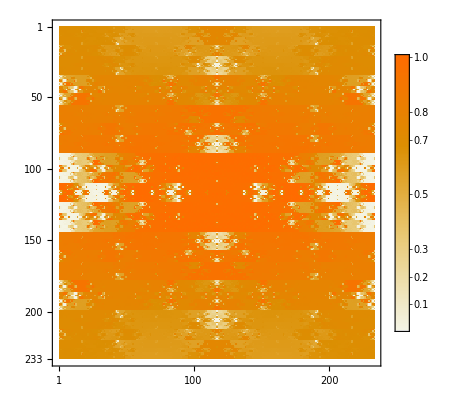

```mathematica
MatrixPlot[comparemol^-1,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
(*Manipulate[ListPlot[comparemol[[a]],Epilog->{Thick,Red,Line[{{0,1-ρ^2/2},{Fibonacci[n+2],1-ρ^2/2}}]},PlotRange->{1-ρ^2,1+ρ^2},Joined->False],{a,1,Fibonacci[n+2],1}]*)
```

```mathematica
om=N[GoldenRatio^-1];
```

#### Atoms

```mathematica
(* evaluate λ numerically, site by site *)
(* select molecular sites at molecular energies *)
at=Range[Fibonacci[n]+1,Fibonacci[n+1]];
atN=intm[[at,at]];
```

```mathematica
(* compute intensity numerically, at finite ρ *)
ρ=0.1;
n=13-3;
{valp,vecp}=Eigensystem[hk[0.,n,ρ,1.]];
{valm,vecm}=Eigensystem[hk[N[Pi/2],n,ρ,1.]];
{vala,veca}=Eigensystem[hk[N[Pi],n,ρ,1.]];
val={valp,valm,vala};
vec={vecp,vecm,veca};
int={};
For[i=1,i<4,i++,
curval=val[[i]];
curvec=vec[[i]];
o=Ordering[curval];
val[[i]]=curval[[o]];
vec[[i]]=curvec[[o]];
AppendTo[int,Abs[vec[[i]]]^2];
]

(* evaluate the integral over k using Simpson's method *)
intm=(int[[1]]+4 int[[2]]+int[[3]])/6;
```

```mathematica
compareat=(atN)/intm;
```

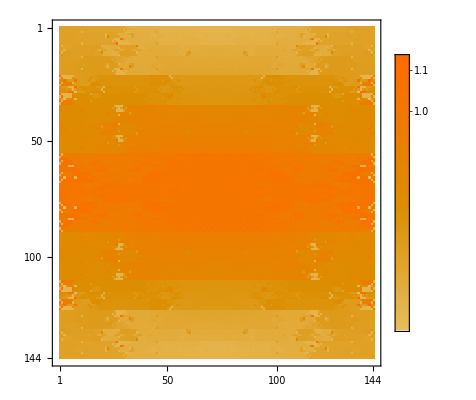

```mathematica
MatrixPlot[compareat^-1,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
Manipulate[ListPlot[comparemol[[a]],Epilog->{Thick,Red,Line[{{0,1-2 ρ^2},{Fibonacci[n+2],1-2 ρ^2}}]},PlotRange->{1-3 ρ^2,1+ρ^2},Joined->False],{a,1,Fibonacci[n+2],1}]
```

Part::partd: Part specification comparemol ⟦ 89 ⟧ is longer than depth of object.

ListPlot::prng: Value of option PlotRange -> {1 - 3\ ρ^2, 1 + ρ^2} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: comparemol ⟦ 89 ⟧ is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {1 - 3\ ρ^2, 1 + ρ^2} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: comparemol ⟦ 89 ⟧ is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {1 - 3\ ρ^2, 1 + ρ^2} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot :: prng will be suppressed during this calculation.

ListPlot::lpn: comparemol ⟦ 89 ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.